<<MaTeX.b4

Failure[…]

```mathematica
<<MaTeX`
```

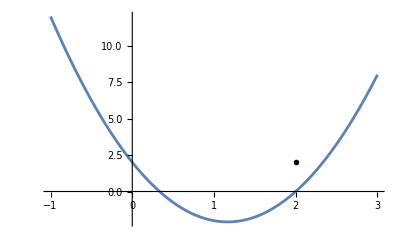

```mathematica
cadena1=MaTeX["x_{1}=2",FontSize->12];
Plot[3 x^2-7x+2,{x,-1,3},Epilog->Text[cadena1,{2,2}]]
```

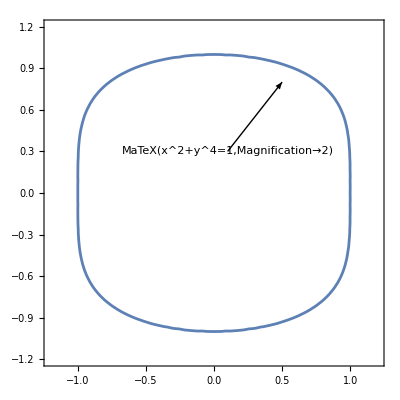

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};

ContourPlot[x^2+y^4==1,{x,-1.2,1.2},{y,-1.2,1.2},BaseStyle->texStyle,Epilog->{Arrow[{{0.1,0.3},{0.5,0.80}}],Inset[MaTeX["x^2+y^4=1",Magnification->2],{0.1,0.3},Scaled[{0.5,1}]]}]
```

```mathematica
MaTeX["\\sum_{k=1}^{\\infty} \\frac{1}{k}"]
```

MaTeX[\sum_{k=1}^{\infty} \frac{1}{k}]

```mathematica
<<MaTeX`
```

```mathematica
MaTeX["\\sum_{k=1}^{\\infty} \\frac{1}{k}"]
```

-Graphics-

```mathematica
cadena1=MaTeX["x_{1}=2",FontSize->12];
Plot[3 x^2-7x+2,{x,-1,3},Epilog->Text[cadena1,{2,2}]]
```

-Graphics-